```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L)));
fr =((2/H)*(1-(r/H)));
a={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H>w>0,w>r>0, w>d>0};

I1=Simplify[Integrate[Integrate[fd*fr,{d,0,w},Assumptions->a],{r,0,w},Assumptions->a],a];

D1=Simplify[Dt[I1,w,Constants -> {L, H}],a];
CDF1 = I1
PDF1 = D1
```

((2 H-w) (2 L-w) w^2)/(H^2 L^2)

(2 w (4 H L-3 H w-3 L w+2 w^2))/(H^2 L^2)

```mathematica
b ={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H,w>H>d >0, w>r>0,w>d>0, H> 0, L> 0, L > w};

I2=Apart[Simplify[Integrate[Integrate[fd*fr,{d,H,w},Assumptions->b],{r,0,H},Assumptions->b]]];
D2=FullSimplify[Dt[I2,w,Constants -> {L, H}],b];

CDF2 = FullSimplify[I2+ Function[w, Evaluate[CDF1]][H],b]
PDF2 = D2
```

((2 L-w) w)/L^2

(2 (L-w))/L^2

```mathematica
mean = Simplify[Integrate[w * PDF1, {w, 0, H}]  + Integrate[w * PDF2, {w, H, L}] ] 
CForm[mean]
```

-(H^3-5 H^2 L-10 L^3)/(30 L^2)

-(Power(H,3) - 5*Power(H,2)*L - 10*Power(L,3))/(30.*Power(L,2))

```mathematica
TeXForm[mean]
```

-\frac{H^3-5 H^2 L-10 L^3}{30 L^2}

```mathematica
variance = Simplify[Integrate[((w - mean)^2 )* PDF1, {w, 0, H}]  + Integrate[(w - mean)^2 * PDF2, {w, H, L}]] 
CForm[variance]
```

-(H^6-10 H^5 L+55 H^4 L^2-140 H^3 L^3+100 H^2 L^4-50 L^6)/(900 L^4)

-(Power(H,6) - 10*Power(H,5)*L + 55*Power(H,4)*Power(L,2) - 140*Power(H,3)*Power(L,3) + 
      100*Power(H,2)*Power(L,4) - 50*Power(L,6))/(900.*Power(L,4))

```mathematica
TeXForm[variance]
```

-\frac{H^6-10 H^5 L+55 H^4 L^2-140 H^3 L^3+100 H^2 L^4-50 L^6}{900 L^4}

```mathematica
CForm[Evaluate[PDF1]]
```

(2*w*(4*H*L - 3*H*w - 3*L*w + 2*Power(w,2)))/(Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[PDF2]]
```

(2*(L - w))/Power(L,2)

```mathematica
CForm[Evaluate[CDF1]]
```

((2*H - w)*(2*L - w)*Power(w,2))/(Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[CDF2]]
```

((2*L - w)*w)/Power(L,2)

```mathematica
TeXForm[Evaluate[CDF1]]
```

\frac{w^2 (2 H-w) (2 L-w)}{H^2 L^2}

```mathematica
TeXForm[Evaluate[CDF2]]
```

\frac{w (2 L-w)}{L^2}

```mathematica
TeXForm[Evaluate[PDF1]]
```

\frac{2 w \left(4 H L-3 H w-3 L w+2 w^2\right)}{H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF2]]
```

\frac{2 (L-w)}{L^2}

1

2

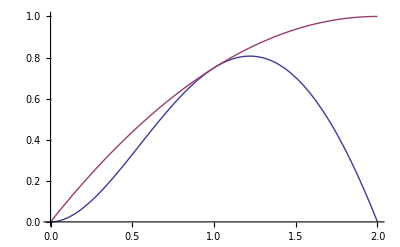

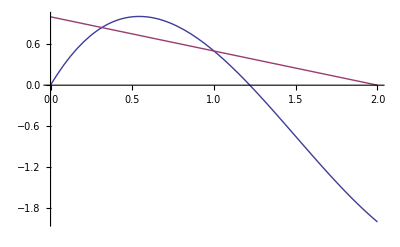

```mathematica
H=1
L=2
Plot[{CDF1,CDF2},{w,0,L }]
Plot[{PDF1,PDF2},{w,0,L}]
```

3

4

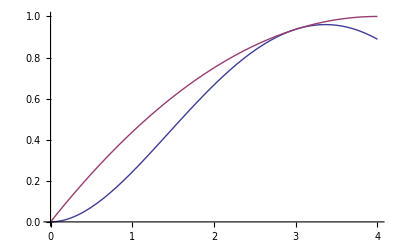

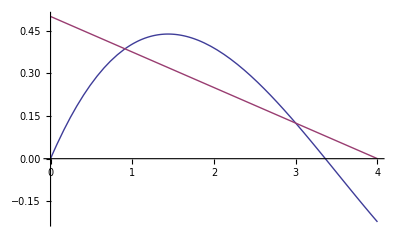

```mathematica
H=3
L=4
Plot[{CDF1,CDF2},{w,0,L }]
Plot[{PDF1,PDF2},{w,0,L  }]
```

5

12

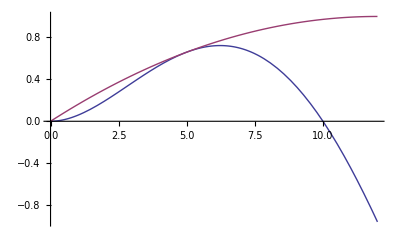

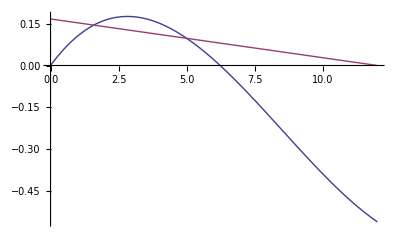

```mathematica
H=5
L=12
Plot[{CDF1,CDF2,CDF3},{w,0,L}]
Plot[{PDF1,PDF2,PDF3},{w,0,L}]
```